```mathematica
(*Quit[];*)
```

```mathematica
(*CloseKernels[]*)
```

{}

```mathematica
FindAverage[fun_,a_,b_]:=(1/(b-a))*NIntegrate[fun,{t,a,b},WorkingPrecision->4, AccuracyGoal-> 4];
```

First we need to define our system of equations sans mutants:

```mathematica
payoffs={x*(γ* α−x),
x*( γ* (1-α^(1/c))^c −x),
x*(γ* αg−x),
γ*x*(1−α),
γ*x*(1−(1-α^(1/c))^c),
γ*x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

What if the second specialist host is not evolving?

```mathematica
{pi,pi2,pig,ψ,ψ2,ψg}=payoffs;
{pi12,pi22,pig2,ψ12,ψ22,ψg2}=payoffs/.{α-> α2,γ-> γ2,x-> x2};
(*Mutant Values*)
```

```mathematica
S1 = v1*ψ+v2*ψ2+(1−v1−v2)*ψg; (*Symbiont 1 *)
S2 =  v1*ψ22+v2*ψ12+(1−v1−v2)*ψg; (*Symbiont 2 *)

Sbar = u1*S1+u2*S2 ;
(*Average Symbiont Payoff*)
```

```mathematica
H1=u1*pi +u2*pi22; (*Host 1 *)
H2 = u1*pi2+u2*pi12;(*Host 2 *)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2+(1-v1-v2)*HG;(*Payoff received by a host on average*)
```

```mathematica
S1D = u1(S1-Sbar);
S2D = u2(S2-Sbar);
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar); (*Host 2*)
```

```mathematica
replicators={S1D,S2D,V1,V2}/.{v1-> v1[t],v2-> v2[t], u1-> u1[t], u2-> u2[t]};
```

```mathematica
ClearAll[u0,v10,v20,c]
{u1'[t]==replicators[[1]],u2'[t]==replicators[[2]],v1'[t]==replicators[[3]],v2'[t]==replicators[[4]],u1[0]==u10,u2[0]==u20,v1[0]==v10,v2[0]==v20};
```

```mathematica
SystemNMG[α_,α2_, αg_,c_,x_,x2_,γ_,γ2_,u10_,u20_,v10_,v20_]:={u1'[t]==u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])),u2'[t]==u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])),v1'[t]==v1[t] (x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]-(x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]) v1[t]-x (-x+αg γ) (1-v1[t]-v2[t])-(x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]) v2[t]),v2'[t]==v2[t] (x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]-(x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]) v1[t]-x (-x+αg γ) (1-v1[t]-v2[t])-(x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]) v2[t]),u1[0]==u10,u2[0]==u20,v1[0]==v10,v2[0]==v20,
(*Conditional statements that stores when extrema occur. This will be necessary to find the period of cycles later: *)
WhenEvent[v1'[t]==0,Sow[{t,v1[t]}], "DetectionMethod"-> "Interpolation"],
(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)


WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u1[t]<0, u1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]<0, u2[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u1[t]>1, u1[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1, u2[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

```mathematica
(**************************** Symbiont 2 Mutant: ***********************************)
```

```mathematica
payoffs={x*(γ* α−x),
x*( γ* (1-α^(1/c))^c −x),
x*(γ* αg−x),
γ*x*(1−α),
γ*x*(1−(1-α^(1/c))^c),
γ*x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

Now h1, h2, mh1, and mh2 each need their own payoffs:

```mathematica
{pi1match,pi1mismatch,pig,ψ1match,ψ1mismatch,ψg}=payoffs;
{pi1MUmatch,pi1MUmismatch,pigna,ψ1MUmatch,ψ1MUmismatch,ψgna}=payoffs/.{α-> αm,γ-> γm,x-> xm};
{pi2match,pi2mismatch,pigna,ψ2match,ψ2mismatch,ψgna}=payoffs/.{α-> α2,γ-> γ2,x-> x2};
{pi2MUmatch,pi2MUmismatch,pigna,ψ2MUmatch,ψ2MUmismatch,ψgna}=payoffs/.{α-> α2m,γ-> γ2m,x-> x2m};
(*2 denotes symbiont 2, 1 denotes symbiont 1*)
(*Mutant Values*)
```

Now expressions for the fitness of s1 and s2 mutants:

```mathematica
S1 = v1*ψ1match+v2*ψ1mismatch+(1−v1−v2)*ψg; (*Symbiont 1 u1 *)
S1M = v1*ψ1MUmatch+v2*ψ1MUmismatch+(1−v1−v2)*ψg; (*Mutant Symbiont 1 u1m*)
S2 =  v1*ψ2mismatch+v2*ψ2match +(1−v1−v2)*ψg; (*Symbiont 2 u2*)
S2M =  v1*ψ2MUmismatch +v2*ψ2MUmatch+(1−v1−v2)*ψg; (*Mutant Symbiont 2 u2m*)
```

Now we need two average frequency expressions, one with s1 mutants, and one with s2 mutants:

```mathematica
SbarM1 = u1*S1+u1m*S1M+u2*S2 ;(*Average Symbiont Payoff*)
SbarM2 = u1*S1+u2*S2+u2m*S2M ;(*Average Symbiont Payoff*)
```

We will also have two expressions for host payoff and frequency:

```mathematica
H1=u1*pi1match +u1m*pi1MUmatch+u2*pi2mismatch;(*Host 1 *)
H2 = u1*pi1mismatch+u1m*pi1MUmismatch+u2*pi2match;(*Host 2 *)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2(*+(1-v1-v2)*HG*);(*Payoff received by a host on average*)
```

```mathematica
S1D = u1(S1-SbarM1);
SM1=u1m(S1M-SbarM1);
S2D = u2(S2-SbarM1);
(*S2D= u1(S1-Sbar);(*Symbiont 1*)*)
(*S2D =u2*(S2-Sbar);*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar);
```

```mathematica
replicators={S1D,S2D,SM1,  V1,V2}/.{v1-> v1[t],v2-> v2[t], u1-> u1[t],u2-> u2[t],u1m-> u1m[t]};
```

```mathematica
ClearAll[v20,v10]
{u1'[t]==replicators[[1]],u2'[t]==replicators[[2]],u1m'[t]==replicators[[3]],v1'[t]==replicators[[4]],v2'[t]==replicators[[5]],u1[0]==u10,u2[0]==u20,u1m[0]==u1m0,v1[0]==v10,v2[0]==v20};
```

```mathematica
SystemINV1[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]:={u1'[t]==u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u1m[t] (xm (1-αm) γm v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+xm (1-(1-αm^(1/c))^c) γm v2[t])),u2'[t]==u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u1m[t] (xm (1-αm) γm v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+xm (1-(1-αm^(1/c))^c) γm v2[t])),u1m'[t]==u1m[t] (xm (1-αm) γm v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+xm (1-(1-αm^(1/c))^c) γm v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u1m[t] (xm (1-αm) γm v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+xm (1-(1-αm^(1/c))^c) γm v2[t])),v1'[t]==v1[t] (x (-x+α γ) u1[t]+xm (-xm+αm γm) u1m[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]-(x (-x+α γ) u1[t]+xm (-xm+αm γm) u1m[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]) v1[t]-(x (-x+(1-α^(1/c))^c γ) u1[t]+xm (-xm+(1-αm^(1/c))^c γm) u1m[t]+x2 (-x2+α2 γ2) u2[t]) v2[t]),v2'[t]==v2[t] (x (-x+(1-α^(1/c))^c γ) u1[t]+xm (-xm+(1-αm^(1/c))^c γm) u1m[t]+x2 (-x2+α2 γ2) u2[t]-(x (-x+α γ) u1[t]+xm (-xm+αm γm) u1m[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]) v1[t]-(x (-x+(1-α^(1/c))^c γ) u1[t]+xm (-xm+(1-αm^(1/c))^c γm) u1m[t]+x2 (-x2+α2 γ2) u2[t]) v2[t]),u1[0]==u10,u2[0]==u20,u1m[0]==u1m0,v1[0]==v10,v2[0]==v20,
(*Conditional statements that stores when extrema occur. This will be necessary to find the period of cycles later: *)
WhenEvent[v1'[t]==0,Sow[t]],
(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)


WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u1[t]<0, u1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]<0, u2[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]<0, u1m[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u1[t]>1, u1[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1, u2[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]>1, u1m[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

```mathematica
H1=(u1)*pi1match +(u2)*pi2mismatch+u2m*pi2MUmismatch;(*Host 1 *)
H2 = (u1)*pi1mismatch+(u2)*pi2match+u2m*pi2MUmatch;(*Host 2 *)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2(*+(1-v1-v2)*HG*);(*Payoff received by a host on average*)
```

```mathematica
S2D = u2(S2-SbarM2);
SM2=u2m(S2M-SbarM2);
S1D= u1(S1-SbarM2);(*Symbiont 1*)
(*S2D =u2*(S2-Sbar);*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar);
```

```mathematica
replicators={S1D,S2D, SM2, V1,V2}/.{v1-> v1[t],u1-> u1[t],v2-> v2[t], u2-> u2[t],u2m-> u2m[t]};
```

```mathematica
{u1'[t]==replicators[[1]],u2'[t]==replicators[[2]],u2m'[t]==replicators[[3]],v1'[t]==replicators[[4]],v2'[t]==replicators[[5]],u1[0]==u10,u2m[0]==u2m0,u2[0]==u20,v1[0]==v10,v2[0]==v20};
```

```mathematica
SystemINV2[α_,α2m_,α2_, αg_,c_,x_,x2m_,x2_,γ_,γ2m_,γ2_,u10_,u20_,u2m0_,v10_,v20_]:={u1'[t]==u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2m (1-α2m) γ2m v2[t])),u2'[t]==u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2m (1-α2m) γ2m v2[t])),u2m'[t]==u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2m (1-α2m) γ2m v2[t]-u1[t] (x (1-α) γ v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) γ v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m v1[t]+x (1-αg) γ (1-v1[t]-v2[t])+x2m (1-α2m) γ2m v2[t])),v1'[t]==v1[t] (x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]+x2m (-x2m+(1-α2m^(1/c))^c γ2m) u2m[t]-(x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]+x2m (-x2m+(1-α2m^(1/c))^c γ2m) u2m[t]) v1[t]-(x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]+x2m (-x2m+α2m γ2m) u2m[t]) v2[t]),v2'[t]==v2[t] (x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]+x2m (-x2m+α2m γ2m) u2m[t]-(x (-x+α γ) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]+x2m (-x2m+(1-α2m^(1/c))^c γ2m) u2m[t]) v1[t]-(x (-x+(1-α^(1/c))^c γ) u1[t]+x2 (-x2+α2 γ2) u2[t]+x2m (-x2m+α2m γ2m) u2m[t]) v2[t]),u1[0]==u10,u2m[0]==u2m0,u2[0]==u20,v1[0]==v10,v2[0]==v20,
(*Conditional statements that stores when extrema occur. This will be necessary to find the period of cycles later: *)
WhenEvent[v1'[t]==0,Sow[t]],
(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)

WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]<0, u2m[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]<0, u2[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]>1, u2m[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1, u2[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

```mathematica
(****************A slightly higher version of ar2 ****************)
am4=ar2+d2;
sol7=NDSolve[SystemINV2[(*Values of α: *)ar1(*α match*),am4(*α2m match*),ar2(*α2*),aag(*αg*),(*c: *)c1,(*values of x: *)0.5 (*x*),0.5(*x2m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γ2m*),1(*γ2*),(*Initial Frequencies: *)u1f,u2fm(*u20*),m21a(*u2m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u2m,v1,v2},{t,0,10*TF},Method->{"Shooting"}];
```

```mathematica
{u1ans,u2ans,m2ans,v1ans,v2ans}= {u1[t],u2[t],u2m[t],v1[t],v2[t]}  /.Flatten[sol7];
avg4=FindAverage[m2ans,5*TF,10*TF];
If[avg4>m21a, 1,0]
```

```mathematica
ClearAll[αr1,αr2,ag,c,d,p,s,u10,u20,v100,v200,solution,timesa,sol,values,T1,TF]

VectorSymbFN2[lαr1_,hαr1_,lαr2_,hαr2_,ag_,c_, d_, p_,s_]:=
ParallelTable[{

αr1,αr2,

u10=0.34;
u20=0.66;
v100=0.66;
v200=0.34;
(*************************** System Before Invasion: *****************************)

solution=
(*SystemNMG[α_,α2_, αg_,c_,x_,x2_,γ_,γ2_,u10_,u20_,v10_,v20_]*)
Reap[NDSolve[SystemNMG[αr1(*α*),αr2(*α2*), (*αg*)ag,(*c*)c,(*x*)0.5,(*x2*)0.5,(*γ*)1,(*γ2*)1,(*u10*)u10,(*u10*)u20,(*v10*)v100,(*v20*)v200],{u1,u2, v1, v2}, {t,0,10000},Method->{"Shooting"}, MaxSteps -> 10^6, WorkingPrecision->MachinePrecision]];
sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)

timesa=Flatten[solution[[2]],1][[All,1]];
values=Flatten[solution[[2]],1][[All,2]];

If[ Length[timesa]<4||Mean[values]<0.0000001||Mean[values]>0.999, times ={1000,1200,1400,1600,1800,2000}, times=timesa ];


T1=2*Median[Differences[Drop[Flatten[times],1]]];

TF=Abs[T1],
{u1f,u2f,v1f,v2f}={u1[3000],u2[3000],v1[3000],v2[3000]}/.Flatten[sol];    
{u1ans,u2ans,v1ans,v2ans}= {u1[t],u2[t],v1[t],v2[t]}/.Flatten[sol];          
Which[ (*Test 1*) T1==400 &&FindAverage[u1ans,3000,3400]>0.9, 

(*Value 1*)SampleInvasion = {


				   
m11=0.05;
u1fm=Abs[u1f-m11];

(************************** A slightly lower ar1: **************************)
αm1=αr1-d;

 (*[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]*)
sol4=NDSolve[SystemINV1[αr1(*α match*), αm1 (*αm match*),αr2(*α2*), ag(*αg*),(*c: *)c,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),u2f,m11(*u1m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u1m,v1,v2},{t,0,10*TF},Method->{"Shooting"},MaxSteps -> 10^6, WorkingPrecision->MachinePrecision];

{u1ans,u2ans,m1ans,v1ans,v2ans}= {u1[t],u2[t],u1m[t],v1[t],v2[t]}  /.Flatten[sol4];

avg1=FindAverage[m1ans, 5*TF,10*TF];
If[avg1>m11, 1,0],

(***************A slightly higher version of ar1: ****************)
αm2=αr1+d;
 (*[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]*)
sol5=NDSolve[SystemINV1[αr1(*α match*), αm2 (*αm match*),αr2(*α2*), ag(*αg*),(*c *)c,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),u2f,m11(*u1m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u1m,v1,v2},{t,0,10*TF},Method->{"Shooting"}, MaxSteps -> 10^6, WorkingPrecision->MachinePrecision];

{uans,m1ans,v1ans,v2ans}= {u1[t],u1m[t],v1[t],v2[t]}  /.Flatten[sol5];
avg2=FindAverage[m1ans,5*TF,10*TF];

If[avg2>m11, 1,0],


avg3=0,

avg4=0},



 (*Test 2 *)T1==400 &&FindAverage[u1ans, 3000,3400]<0.9,


(*Value 2*)
SampleInvasion ={     
				  
m21=0.05;
u2fm =Abs[u2f-m21];

avg1=0,

avg2=0,

(********************** A slightly lower version of ar2 *********************)
αm3=αr2-d;
 (*[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]*)
sol6=NDSolve[SystemINV2[(*Values of α: *)αr1(*α match*),αm3(*α2m match*),αr2(*α2*),ag(*αg*),(*c: *)c,(*values of x: *)0.5 (*x*),0.5(*x2m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γ2m*),1(*γ2*),(*Initial Frequencies: *)u1f(*u10*),u2fm(*u2m0*),m21(*u2m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u2m,v1,v2},{t,0,10*TF},Method->{"Shooting"}, MaxSteps -> 10^6, WorkingPrecision->MachinePrecision];

{u1ans,u2ans,m2ans2,v1ans,v2ans}= {u1[t],u2[t],u2m[t],v1[t],v2[t]}  /.Flatten[sol6];
avg3=FindAverage[m2ans2, 5*TF,10*TF];
If[avg3>m21, 1,0],


(****************A slightly higher version of ar2 ****************)
αm4=αr2+d;
sol7=NDSolve[SystemINV2[(*Values of α: *)αr1(*α match*),αm4(*α2m match*),αr2(*α2*),ag(*αg*),(*c: *)c,(*values of x: *)0.5 (*x*),0.5(*x2m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γ2m*),1(*γ2*),(*Initial Frequencies: *)u1f,u2fm(*u20*),m21(*u2m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u2m,v1,v2},{t,0,10*TF},Method->{"Shooting"}, MaxSteps -> 10^6, WorkingPrecision->MachinePrecision];
{u1ans,u2ans,m2ans,v1ans,v2ans}= {u1[t],u2[t],u2m[t],v1[t],v2[t]}  /.Flatten[sol7];
avg4=FindAverage[m2ans,5*TF,10*TF];


If[avg4>m21, 1,0]} , (*Test 3*) TF ≠ 400, (*Value 3: *)



SampleInvasion = Table[{
(********************** Initial Conditions for Invasion ***********************)

				   
m11=0.05*u1f;
m21=0.05*u2f;

u1fm=u1f-m11;
u2fm=u2f-m21;

(************************ A slightly lower ar1: ***************************)
αm1=αr1-d;
 (*[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]*)
sol4=NDSolve[SystemINV1[αr1(*α match*), αm1 (*αm match*),αr2(*α2*), ag(*αg*),(*c: *)c,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),u2f,m11(*u1m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u1m,v1,v2},{t,0,10*TF},Method->{"Shooting"} ,MaxSteps -> 10^6, WorkingPrecision->MachinePrecision];

{u1ans,u2ans,m1ans,v1ans,v2ans}= {u1[t],u2[t],u1m[t],v1[t],v2[t]}  /.Flatten[sol4];

avg1=FindAverage[m1ans, 5*TF,10*TF];
If[avg1>m11, 1,0],

(***************A slightly higher version of ar1: ****************)
αm2=αr1+d;
 (*[α_,αm_,α2_, αg_,c_,x_,xm_,x2_,γ_,γm_,γ2_,u10_,u20_,u1m0_,v10_,v20_]*)
sol5=NDSolve[SystemINV1[αr1(*α match*), αm2 (*αm match*),αr2(*α2*), ag(*αg*),(*c *)c,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),u2f,m11(*u1m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u1m,v1,v2},{t,0,10*TF},Method->{"Shooting"}, WorkingPrecision->MachinePrecision, MaxSteps -> 10^6];

{uans,m1ans,v1ans,v2ans}= {u1[t],u1m[t],v1[t],v2[t]}  /.Flatten[sol5];
avg2=FindAverage[m1ans,5*TF,10*TF];

If[avg2>m11, 1,0],


(********************** A slightly lower version of ar2 *********************)
αm3=αr2-d;
(*[α_,α2m_,α2_, αg_,c_,x_,x2m_,x2_,γ_,γ2m_,γ2_,u10_,u20_,u2m0_,v10_,v20_]*)
sol6=NDSolve[SystemINV2[(*Values of α: *)αr1(*α match*),αm3(*α2m *),αr2(*α2*),ag(*αg*),(*c: *)c,(*values of x: *)0.5 (*x*),0.5(*x2m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γ2m*),1(*γ2*),(*Initial Frequencies: *)u1f(*u10*),u2fm(*u2m0*),m21(*u2m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u2m,v1,v2},{t,0,10*TF},Method->{"Shooting"},WorkingPrecision->MachinePrecision, MaxSteps -> 10^6];


{m2ans2,u2ans,v1ans,v2ans}= {u2m[t],u2[t],v1[t],v2[t]}  /.Flatten[sol6];
avg3=FindAverage[m2ans2, 5*TF,10*TF];
If[avg3>m21, 1,0],




(****************A slightly higher version of ar2 ****************)
αm4=αr2+d;
(*[α_,α2m_,α2_, αg_,c_,x_,x2m_,x2_,γ_,γ2m_,γ2_,u10_,u20_,u2m0_,v10_,v20_]*)
sol7=NDSolve[SystemINV2[(*Values of α: *)αr1(*α match*),αm4(*α2m match*),αr2(*α2*),ag(*αg*),(*c: *)c,(*values of x: *)0.5 (*x*),0.5(*x2m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γ2m*),1(*γ2*),(*Initial Frequencies: *)u1f,u2fm(*u20*),m21(*u2m0*),v1f(*v10*),v2f(*v20*)], {u1,u2,u2m,v1,v2},{t,0,10*TF},Method->{"Shooting"}, WorkingPrecision->MachinePrecision, MaxSteps -> 10^6];
{u1ans,u2ans,m2ans,v1ans,v2ans}= {u1[t],u2[t],u2m[t],v1[t],v2[t]}  /.Flatten[sol7];
avg4=FindAverage[m2ans,5*TF,10*TF];
If[avg4>m21, 1,0]



},
(*******************   Invade the Resident Period      ************************)
{st,3000+(p*T1),3000+T1,p*T1}];
];

lower1=Mean[Take[Flatten[SampleInvasion],{1,-1,4}]],
higher1=Mean[Take[Flatten[SampleInvasion],{2,-1,4}]],
higher1-lower1,
lower2=Mean[Take[Flatten[SampleInvasion],{3,-1,4}]],
higher2=Mean[Take[Flatten[SampleInvasion],{4,-1,4}]],
higher2-lower2

},
{αr1,lαr1,hαr1,s},{αr2,lαr2,hαr2,s}]
```

```mathematica
CCDown1=VectorSymbFN2[0.35,0.95,0.35,0.95,0.3,1/2,0.005, 0.01,0.01];
```

NDSolve::ndsz: At t == 525.073, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 3366.42, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1996.31, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1087.63, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 822.007, step size is effectively zero; singularity or stiff system suspected.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3874.9689167189352391885378320678795516229797613050323}. NIntegrate obtained -8.00987489650551793788660198366476282311028114099284972×10^45 and 2.49942950147503003931675318753265956756583710532964257×10^45 for the integral and error estimates.

NDSolve::ndsz: At t == 2239.46, step size is effectively zero; singularity or stiff system suspected.

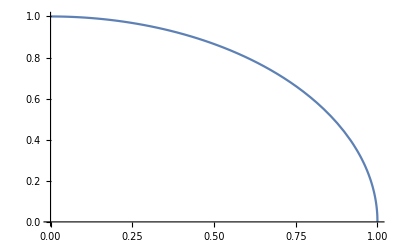

```mathematica
Plot[(1-α^(1/c))^c/.c-> 1/2,{α,0,1}]
```

```mathematica
CCDown2=VectorSymbFN2[0.35,0.70,0.35,0.72,0.35,1/2,0.005, 0.01,0.01];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,1080,14].

KernelObject::rdead: Subkernel connected through … appears dead.

LaunchKernels::clone: Kernel … resurrected as ….

InterpolatingFunction::dmvali: The integration endpoint 4000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 2319.68, step size is effectively zero; singularity or stiff system suspected.

```mathematica
CCDown3=VectorSymbFN2[0.72,0.95,0.72,0.95,0.3,1/2,0.005, 0.01,0.01];
```

NDSolve::ndsz: At t == 108.348, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmvali: The integration endpoint 2000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 4000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 107.644, step size is effectively zero; singularity or stiff system suspected.

```mathematica
CCDown4=VectorSymbFN2[0.72,0.95,0.35,0.70,0.3,1/2,0.005, 0.01,0.01];
```

$Aborted

```mathematica
CCDown=Join[CCDown1,CCDown2,CCDown4];
```

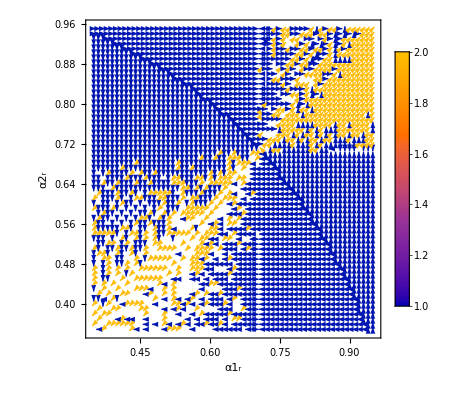

```mathematica
ListVectorPlot[Partition[Partition[Flatten[Flatten[CCDown1,1][[All,{1,2,6,9}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints-> All ]
```

```mathematica
ListInterpolation[Flatten[CCDown1,1][[All,{1,2,6,9}]]]
```

InterpolatingFunction[…]

```mathematica
CCDown2=VectorSymbFN2[0.35,0.71,0.35,0.71,0.3,1/2,0.005, 0.01,0.01];
```

```mathematica
CCDown3=VectorSymbFN2[0.71,0.95,0.35,0.71,0.3,1/2,0.005, 0.01,0.01];
```

```mathematica
CCDown4=VectorSymbFN2[0.71,0.95,0.71,0.95,0.3,1/2,0.005, 0.01,0.01];
```

```mathematica
Down1=Flatten[CCDown1,1];
Down2=Flatten[CCDown2,1];
Down3=Flatten[CCDown3,1];
Down4=Flatten[CCDown4,1];
Together=Join[Down1,Down2,Down3,Down4];
```